```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Angle Maps via the Radon Transform

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

The threads in a weave pattern may not always be exactly horizontal and vertical. The warp and the weft may not be perpendicular to each other. In some cases, the thread lines bend across the width (and/or height) of the patch. This notebook shows how such irregularities may be detected using the Radon transform.

```mathematica
TableForm[{{Hyperlink["CanvasRotation",{"visualVocabAngleMapsRadon.nb","labelCanvasRotation"},BaseStyle->appColor],labelCanvasRotation},{Hyperlink["RadonLine",{"visualVocabAngleMapsRadon.nb","labelRadonLine"},BaseStyle->appColor],labelRadonLine},{Hyperlink["RadonGrid",{"visualVocabAngleMapsRadon.nb","labelRadonGrid"},BaseStyle->appColor],labelRadonGrid},{Hyperlink["RadonRipples",{"visualVocabAngleMapsRadon.nb","labelRadonRipples"},BaseStyle->appColor],labelRadonRipples},{Hyperlink["CircularMask",{"visualVocabAngleMapsRadon.nb","labelCircularMask"},BaseStyle->appColor],labelCircularMask},{Hyperlink["RadonXRay",{"visualVocabAngleMapsRadon.nb","labelRadonXRay"},BaseStyle->appColor],labelRadonXRay},{Hyperlink["RadonPreProc",{"visualVocabAngleMapsRadon.nb","labelRadonPreProc"},BaseStyle->appColor],labelRadonPreProc},{Hyperlink["RadonCompare",{"visualVocabAngleMapsRadon.nb","labelRadonCompare"},BaseStyle->appColor],labelRadonCompare}}]
```

CanvasRotationvisualVocabAngleMapsRadon.nblabelCanvasRotationvisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | It's easy to align the canvas vertically and horizontally by eye
RadonLinevisualVocabAngleMapsRadon.nblabelRadonLinevisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | The Radon transform (right) shows the location and orientation of the line (left)
RadonGridvisualVocabAngleMapsRadon.nblabelRadonGridvisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | The Radon transform (right) shows the locations and orientations of the lines (left)
RadonRipplesvisualVocabAngleMapsRadon.nblabelRadonRipplesvisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | The location of the ripples in the Radon transform (right) shows the angle of the image
CircularMaskvisualVocabAngleMapsRadon.nblabelCircularMaskvisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | Masking the edges removes the V structures
RadonXRayvisualVocabAngleMapsRadon.nblabelRadonXRayvisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | Applying the Radon transform to the x-ray tiles shows the same ripples as the model
RadonPreProcvisualVocabAngleMapsRadon.nblabelRadonPreProcvisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | Applying various kinds of preprocessing (such as thresholding) may help
RadonComparevisualVocabAngleMapsRadon.nblabelRadonComparevisualVocabAngleMapsRadon.nbHyperlinkHyperlinkActive | Compare the rotation (as calculated by the Radon transform) with a value done by hand

The most important functions in this notebook are the RadonTransform[ ] and its inverse. ImageRotate[ ] is used to rotate the images and ImageMultiply[ ] is used to mask the images.

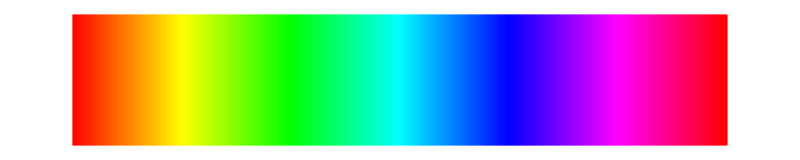

```mathematica
specLine
```

The issues with rotated and bent threads can be seen in the following demonstration, which uses the "rotation in degrees" slider to rotate the image. The green lines are true horizontal and vertical, and can be used as a guide to visually line up the rotated threads. For example, F634Tile becomes vertical when it is rotated about 1°. In L10, the vertical threads are about -5° from true vertical while the horizontal threads are less than 2° from true horizontal. Moreover, the threads bend differently in the left half of the image from the right half. As usual, the option key allows smoother motion when changing parameter values.

```mathematica
labelCanvasRotation="It's easy to align the canvas vertically and horizontally by eye";
infoCanvasRotation="The threads in a weave pattern may not always be exactly horizontal and vertical; the warp and weft may not be perpendicular.\n\nRotate the image (using the 'rotation in degrees' slider) until the vertical and horizontal threads align visually with the green crosshairs.\n\nThe 2D controller moves the crosshairs around for easiler comparison.\n\nFor example, F634Tile becomes vertical when it is rotated about 1°.\n\nIn RSM_r042520, the horizontal threads are about -2.8° from true horizontal while the vertical threads are less than 1° from true vertical.\n\nIn L10, the threads bend differently in the left half of the imge from the right half. What measurements do you get?\n\nAs usual, the option key allows smoother motion when changing parameter values on all parameters.";
Manipulate[Module[{img},
If[invert=="positive",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];Show[Image[ImageRotate[ColorNegate[img],Pi θ/180],ImageSize->420],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{0,thisRowCol[[2]]},{tileSize,thisRowCol[[2]]}}]}],Graphics[{Green,Opacity[0.4],Thickness[0.02],Line[{{thisRowCol[[1]],0},{thisRowCol[[1]],tileSize}}]}]]],Row[{Column[{Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[20],info[infoCanvasRotation]}],Control[{{θ,0,"rotation in degrees"},-30,30,Appearance->"Labeled"}]}],Control[{{thisRowCol,{tileSize/2,tileSize/2},""},{1,1},{tileSize,tileSize},1}]}],
FrameLabel->Style[labelCanvasRotation,Medium],TrackedSymbols->{i,θ,thisRowCol,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

The Radon transform is a way of projecting through an image at all angles and summing. This section shows how the Radon transform can be used to locate the orientation (or rotation) of an image such as the weave patterns in canvas x-rays. To see what Radon transforms show, consider the Radon transform of a single line, as in the following picture. The left hand image shows the line, while the right hand image shows the Radon transform. In this example, the Radon transform is a bright dot in the plane: as the line moves left and right, the bright dot moves up and down, As the line tilts away from vertical, the bright dot moves left and right. The position of the maximum gives both the location and orientation of the line.

```mathematica
labelRadonLine="The Radon transform (right) shows the location and orientation of the line (left)";
infoRadonLine="A line in an image (on the left) corresponds to a bright spot in the Radon transform (on the right). Play with the position and angle of the line: here is what you will find:\n\nThe angle of the line corresponds to the horizontal position of the white dot in the tranformed space.\n\nThe left/right position of the line corresponds to the vertical height of the white dot in the transformed space.";Manipulate[img=Image[Graphics[{White,Thickness->0.02,Line[{{ρ Cos[θ]+30 Sin[θ],ρ Sin[θ]-30 Cos[θ]},{ρ Cos[θ]-30 Sin[θ],ρ Sin[θ]+30 Cos[θ]}}]},AxesOrigin->{0,0},PlotRange->{{-30,30},{-30,30}},Background->Black]];
GraphicsGrid[{{img,ImageAdjust[Radon[img,Method->"Hough"]]}}],
{{ρ,0,"position of the line"},0,30},Row[{Control[{{θ,0,"angle of the line"},-Pi/2,Pi/2}],Spacer[20],info[infoRadonLine]}],
FrameLabel->Style[labelRadonLine,Medium],TrackedSymbols->{ρ,θ},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

It works for many lines too, which is why it can work for a grid of values like a series of lines. When the two collections of lines are orthogonal, there are two columns of bright points, one forming a straight line of points at the angle of the vertical (visible at 90°, in the middle of transform figure) and one forming a line of points at 0°, the line of points at the left (and right) hand edges. As the angles deviate from orthogonal, one or both of the columns of bright dots moves. In all cases, they track the angle of the parallel lines, and so can be used to locate both the rotation and the skew of the figure.

```mathematica
labelRadonGrid="The Radon transform (right) shows the locations and orientations of the lines (left)";
infoRadonGrid="Each of the lines in the image on the left corresponds to one of the bright spots in the Radon transform on the right.\n\nThe first angle is the angle of the (roughly) vertical lines in the grid. Changing this moves the central column of spots to the left or right (depending on whether the angle is greater than or less than 90°.\n\nThe second angle is the angle of the (roughly) horizontal lines in the grid. Changing this moves the other column of spots to the left or right (observe the wrap-around: the leftmost portion of the image is adjacent to the rightmost part of the image).\n\nChanging the position of the grid moves the two columns of spots up and down.";Manipulate[img=Image[Graphics[{White,Thickness->0.02,Table[Line[{{(ρ+n) Cos[θ1]+30 Sin[θ1],(ρ+n) Sin[θ1]-30 Cos[θ1]},{(ρ+n) Cos[θ1]-30 Sin[θ1],(ρ+n) Sin[θ1]+30 Cos[θ1]}}],{n,-50,50,15}],Table[Line[{{(ρ+n) Cos[θ2]+30 Sin[θ2],(ρ+n) Sin[θ2]-30 Cos[θ2]},{(ρ+n) Cos[θ2]-30 Sin[θ2],(ρ+n) Sin[θ2]+30 Cos[θ2]}}],{n,-50,50,15}]},AxesOrigin->{0,0},PlotRange->{{-30,30},{-30,30}},Background->Black]];
GraphicsGrid[{{img,ImageAdjust[Radon[img,Method->"Hough"]]}},ImageSize->500],{{ρ,0,"position of the grid"},0,30},{{θ1,0,"first angle"},-Pi/2,Pi/2},Row[{Control[{{θ2,Pi/2,"second angle"},0,Pi}],Spacer[20],info[infoRadonGrid]}],FrameLabel->Style[labelRadonGrid,Medium],TrackedSymbols->{ρ,θ1,θ2},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Consider applying the Radon transform to some of the thread models. After all, if we can’t understand what is happening in these relatively simple models, it will be hard to understand when applied to real data. The next demonstration shows the Radon transform of the rectangle model, the functional model, and an x-ray tile.  In each case, the Radon transform shows two columns of bright points. The one in the center represents the angle of the horizontal threads and the other (which appears half on the left at 0° and half on the right at 360°) represents the angle of the vertical threads.

```mathematica
labelRadonRipples="The location of the ripples in the Radon transform (right) shows the angle of the image";
infoRadonRipples="The Radon transform (right) of various thread-like images (left).\n\nIn each case, the Radon transform shows two columns of bright points. The one in the center represents the angle of the horizontal threads and the other (which appears half on the left at 0° and half on the right at 360°) represents the angle of the vertical threads.\n\nObserve how these columns of bright spots move left and right proportionally as you rotate the image with the rotation slider.\n\nThe functional model has more columns of bright spots (to the left and right of the main two columns. Can you guess the origin of these?\n\nThere are also 45° lines in the shape of a V and an upside-down V. Can you guess what feature of the image these correspond to?";
Manipulate[Module[{img,radImg,imgSmall},If[invert=="positive",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];radImg=ImageAdjust[Radon[imgSmall=ImageTake[ImageRotate[img,Pi θ/180],{200,400},{200,400}]]];
GraphicsRow[{imgSmall,radImg},ImageSize->600]],
Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[10],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[10],Control[{{θ,0,"rotation in degrees"},-45,45,Appearance->"Labeled"}],info[infoRadonRipples]}],
FrameLabel->Style[labelRadonRipples,Medium],TrackedSymbols->{θ,i,invert},SaveDefinitions->saveDef]
```

There are other prominent features of these images (besides the two columns of bright spots). What is the diamond shape in the middle, and the larger structure that looks like a V superimposed on an upside down V? A little thought shows that this is caused by the rectangular shape of the images: when the Radon projects and sums through the image at a 45° angle, there are more pixels and so the sum tends to be larger, irrespective of the contents of the image. Accordingly, it may be advantageous to mask the image.

```mathematica
specLine
```

-Graphics-

A simple way to do this is to create a disk that is 1 at all points inside and 0 at all points outside. Multiplying this disk point-by-point by the image effectively removes all information outside the disk while retaining all data inside. Observe that the diamond and the V structures are now gone from the Radon transform.

```mathematica
labelCircularMask="Masking the edges removes the V structures";
infoCircularMask="The Radon transform (right) of various thread-like images (left).\n\nIn each case, the Radon transform shows two columns of bright points. The one in the center represents the angle of the horizontal threads and the other (which appears half on the left at 0° and half on the right at 360°) represents the angle of the vertical threads.\n\nThe black mask is applied to show that the V (and upside-down V) are caused by the square edges. Hence, from now on, when applying the Radon, we will use such a mask.";
Manipulate[Module[{img,radImg,imgSmall},
If[invert=="positive",img=allIm[[i]],img=ColorNegate[allIm[[i]]]];radImg=ImageAdjust[Radon[imgSmall=ImageMultiply[whiteDisk,ImageTake[ImageRotate[img,Pi θ/180],{201,400},{201,400}]]]];
GraphicsRow[{imgSmall,radImg},ImageSize->600]],Row[{Control[{{i,2,"image"},Thread[Range[Length[allIm]]->allImNames],ControlType->PopupMenu}],Spacer[10],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[10],Control[{{θ,0,"rotation in degrees"},-45,45,Appearance->"Labeled"}],info[infoCircularMask]}],
SynchronousUpdating->False,ContinuousAction->False,FrameLabel->Style[labelCircularMask,Medium],
TrackedSymbols->{θ,i,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

When applying the Radon transform to real images, such as the canvas thread x-rays, there are again two columns of bright points, one representing the angle of the vertical threads and the other representing the angle of the horizontal threads. Masking the image as above removes the two superimposed V shapes.

```mathematica
labelRadonXRay="Applying the Radon transform to the x-ray tiles shows the same ripples as the model";
infoRadonXRay="The masked tiles (left) and their Radon transform (right).\n\nIn almost all cases, the same features are clearly visible as in the simpler models above (i.e, the two columns of larger variation track the vertical and horizontal angles of the weave pattern).\n\nIn many cases, even when the threads cannot be individually discerned, the ridge of ripples is still clear.";
Manipulate[Module[{img,radImg,imgSmall},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];radImg=ImageAdjust[Radon[imgSmall=ImageMultiply[whiteDisk,ImageTake[img,{1,200},{1,200}]]]];
GraphicsRow[{imgSmall,radImg},ImageSize->600]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[10],info[infoRadonXRay]}],
SynchronousUpdating->False,ContinuousAction->False,FrameLabel->Style[labelRadonXRay,Medium],TrackedSymbols->{i,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Sometimes it is possible to bring out features of interest more clearly if the image is binarized before application of the Radon transform.

```mathematica
labelRadonPreProc="Applying various kinds of preprocessing (such as thresholding) may help";
infoRadonPreProc="Sometimes it is possible to bring out features of interest more clearly if the masked image (left) is preprocessed before application of the Radon transform.\n\nThis demonstration binarizes the image (middle) using the threshold set by the slider. Observe that the clarity of the features in the transform (right) changes with the threshold level.\n\nTry several of the tiles and locate the best threshold.\n\nObserve that for F695 there is no threshold that gives the desired ridges in the transform.";
Manipulate[Module[{img,radImg,imgSmall,binImg},
If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];radImg=ImageAdjust[Radon[binImg=Binarize[imgSmall=ImageMultiply[whiteDisk,ImageTake[img,{1,200},{1,200}]],s]]];
GraphicsRow[{imgSmall,binImg,radImg},ImageSize->800]],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"positive",""},{"negative","positive"}}],Spacer[10],Control[{{s,0.5,"threshold"},0,1}],Spacer[20],info[infoRadonPreProc]}],FrameLabel->Style[labelRadonPreProc,Medium],TrackedSymbols->{i,s,invert},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

The next plot resamples the Radon image so that it has 180 columns (one corresponding to each degree). Using the “get coordinates” feature (control/click on the image), it is then clear that the first column of bright spots occurs at 88°, implying that the vertical slope is tilted by 2°, while the right-hand column of bright spots occurs at the 179th column implying that the horizontal threads are tilted about 1°. This compares pretty well with the manual tilting and rotating done above. Thus the columns of the Radon transform where the most bright spots lie are precisely related to the rotation and skew of the threads. This can be used to automatically find the correct rotation.

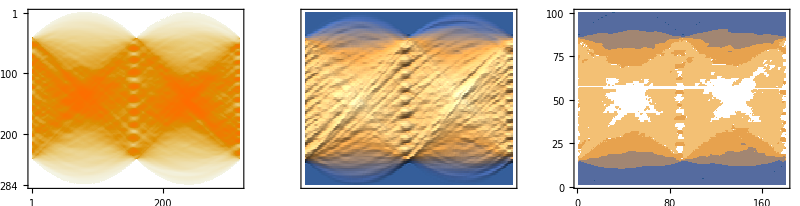
-Graphics-Different views of the Radon transform

```mathematica
radImg=ImageAdjust[Radon[ImageTake[allImagesXray[[f634Tile]],{200,400},{200,400}]]];
Labeled[GraphicsRow[{MatrixPlot[ImageData[radImg]],ReliefPlot[ImageData[ImageResize[radImg,{180,100}]]],ListContourPlot[ImageData[ImageResize[radImg,{180,100}]]]},ImageSize->800],"Different views of the Radon transform"]
```

HW: Take some new images and process with the Radon transform to estimate the rotation. Use these values to do an automated thread count across several different threads. Verify the counts using a hand count, and discuss the sources of error in both procedures.

HW: Explain how to get the Radon transform to give better accuracy than 1°. Implement this method and redo the hand counts from the previous problem.

HW: Would a histogram equalization step prior to the Radon transform help improve the interpretability of the output? Try it!

```mathematica
specLine
```

-Graphics-

To see how this process might be automated, the following code reads in a 2cm by 2cm patch, masks off a circular portion in the center, and then takes the Radon transform. The column towards the middle that is the wiggliest indicates the angle of the weave. To locate this wiggliest column numerically, filter with a low pass kernel in the horizontal direction: this does not effect the wiggliness in the vertical direction, but does smooth things out in the horizontal direction (where the changes are less important). The third image shows the output of this filter; the central spine appears more clearly than in the unfiltered version. The wiggliness of each column is then tested by taking the variance (column-wise). The result here is shown in the plot on the bottom. To find the column with the greatest variance, the code looks for the largest value and then interpolates (to get a slightly more accurate answer). The numbers on the bottom row (the value of the variable near0), show the max value (in this case 0.04) and the location where this max value occurs (in this case, at -0.027 radians). Converting to degrees, this is -1.57°.

```mathematica
img=ImageRotate[allImagesXray[[f634Tile]]];
imgDim=ImageDimensions[img];
sizR=720;
whiteDisk=Rasterize[Graphics[{White,Disk[]},Background->Black],RasterSize->Max[imgDim]];radImg=ImageAdjust[Radon[imgPlot=ColorConvert[ImageMultiply[whiteDisk,img],"Grayscale"],{sizR,600},{-Pi/8,Pi/8}]];
radius=599;
ker=ConstantArray[0,{radius,radius}];
ker[[(radius+1)/2]]=ConstantArray[1,radius]/radius;
filteredRadon=ImageAdjust[ImageSubtract[radImg,ImageAdjust[ImageConvolve[radImg,ker]]]];
varRadonV=Variance[ImageData[filteredRadon]];
stepPer=Pi/(4 Length[varRadonV]);
angles=N[Range[-Pi/8,Pi/8-0.000001,stepPer]];
guess=indMax[varRadonV] stepPer-Pi/8;
interpRadon=Interpolation[Transpose[{angles,varRadonV}]];
near0=FindMaximum[{interpRadon[z],-Pi/8<z<Pi/8},{z,guess},AccuracyGoal->6];
Labeled[GraphicsGrid[{{ImageRotate[imgPlot,-Pi/2],radImg,filteredRadon},{Labeled[Plot[interpRadon[z],{z,-Pi/8,Pi/8},PlotRange->All],"Column Variances"],near0}},ImageSize->600],"The masked tile, the Radon transform, and the result after filtering are shown in the top. The bottom shows the column variances as a function. The desired position is the location of the maximum of this function. This is one way to automatically extract the horizontal position of the column with the greatest variation and hence to locate the angle of the threads.",LabelStyle->captionStyle]
```

-Graphics-The masked tile, the Radon transform, and the result after filtering are shown in the top. The bottom shows the column variances as a function. The desired position is the location of the maximum of this function. This is one way to automatically extract the horizontal position of the column with the greatest variation and hence to locate the angle of the threads.

```mathematica
specLine
```

-Graphics-

Here is a somewhat more user-friendly implementation of this same procedure. Choose the x-ray patch to examine and press the “Estimate Average Rotation” button. The display will show the algorithms best guess for the displayed patch. By moving the green line around (mouse to the two locators on the ends) you can verify whether the calculated angle is close (within a degree or so) to what a human might judge. The Radon method works quite well even when the patches are not very distinct.

```mathematica
labelRadonCompare="Compare the rotation (as calculated by the Radon transform) with a value done by hand";
infoRadonCompare="Using the mouse, move the two endpoints of the green line to line up with a row of the threads in the image. The angle of this line is displayed on the right.\n\nPress the 'Estimate Average Rotation' button and the technique above is used to automatically estimate the angle. The answer is shown as the estimate.\n\nObserve that in most cases, the estimate is close to the manual value.\n\nHow could this same code be used to find the vertical thread angle?";
autoRot[im_]:=Module[{},imgDim=ImageDimensions[im];
sizR=720;
whiteDisk=Rasterize[Graphics[{White,Disk[]},Background->Black],RasterSize->Max[imgDim]];
radImg=ImageAdjust[Radon[ColorConvert[ImageMultiply[whiteDisk,ImageRotate[im]],"Grayscale"],{sizR,600},{-Pi/8,Pi/8}]];
radius=599;
ker=ConstantArray[0,{radius,radius}];
ker[[(radius+1)/2]]=ConstantArray[1,radius]/radius;
filteredRadon=ImageAdjust[ImageSubtract[radImg,ImageAdjust[ImageConvolve[radImg,ker]]]];
varRadon=Variance[ImageData[filteredRadon]];
stepPer=Pi/(4 Length[varRadon]);
angles=N[Range[-Pi/8,Pi/8-0.000001,stepPer]];
guess=indMax[varRadon] stepPer-Pi/8;
If[Abs[guess]>0.3,guess=0;];
interpRadon=Interpolation[Transpose[{angles,varRadon}]];
near0=FindMaximum[interpRadon[z],{z,guess},AccuracyGoal->4,PrecisionGoal->4];
angleDeg=Last[near0][[1,2]] 180/Pi];
slope[s_,e_]:=N[ArcTan[-e[[2]]+s[[2]],e[[1]]-s[[1]]]-Pi/2];
estimate=0;iOld=0;
Manipulate[s=slope[start,end];
len=Norm[start-end];
img=allImagesXray[[i]];
{col,row}=ImageDimensions[img];
If[invert=="negative",imgDisp=img,imgDisp=ColorNegate[img]];
If[showGrid=="show",opac=1,opac=0];
If[estRot===True,estRot=False;estimate=autoRot[img];];
If[i≠iOld,iOld=i;estimate=0;];
dpi=600;dpc=dpi/2.54;
xPos=Table[x,{x,0,col,dpc/2}];
yPos=Table[y,{y,0,row,dpc/2}];
allCols=Transpose[{Flatten[Outer[List,{0},xPos],1],Flatten[Outer[List,{col},xPos],1]}];
allRows=Transpose[{Flatten[Outer[List,yPos,{0}],1],Flatten[Outer[List,yPos,{row}],1]}];
outText="Image:\n"~~imageNamesX[[i]]~~"\nStart: "~~ToString[Round[start]]~~"\nEnd: "~~ToString[Round[end]]~~"\nAngle (deg): "~~ToString[PaddedForm[s/Degree,{3,1}]]~~"\nEstimate of Average\nRotation: "~~ToString[PaddedForm[estimate,{3,1}]];
Row[{Graphics[Show[imgDisp,Graphics[{Green,Opacity[1],Thickness[0.002],Line[{start,end}],Opacity[0.4],Thickness[0.02],Line[{start,end}]}],Graphics[{Yellow,Opacity[opac],Table[Line[allCols[[i]]],{i,1,Length[xPos]}]}],Graphics[{Yellow,Opacity[opac],Table[Line[allRows[[i]]],{i,1,Length[yPos]}]}]]],Spacer[20],Framed[outText]}],{{start,{col/5,row/2}},Locator},{{end,{4 col/5,row/2}},Locator},Row[{Control[{{i,f634Tile,"Image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[5],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],Control[{{showGrid,"hide","Grid"},{"hide","show"}}],Spacer[20],Control[{{estRot,False,"Estimate Average Rotation"},{False,True}}],Spacer[20],info[infoRadonCompare]}],
FrameLabel->Style[labelRadonCompare,Medium],TrackedSymbols->{start,end,showGrid,invert,estRot},SaveDefinitions->saveDef]
```